```mathematica
do=Map[{Chrom[#[[1]]],Chrom[#[[2]]],{#[[1]],#[[2]],Read[StringToStream[#[[3]]],Expression]}}&,Select[deps2,#[[1]]≤260000 && #[[2]]≤260000&]
]; Length[do]
```

27400

```mathematica
Take[do,5]
```

{{24,24,{1,2,{2,1<->4,2<->3}}},{24,24,{2,3,{2,2<->4,3<->5}}},{24,96,{2,4,{2,2<->5,1<->4}}},{24,24,{3,5,{2,1<->5,2<->3}}},{24,96,{3,6,{2,2<->5,1<->6}}}}

```mathematica
ListPlot[Map[{#[[1]],#[[2]]}&,do]]
```

$Aborted

```mathematica
comp=Select[do,#[[1]]>#[[2]]&];Length[comp]
```

3832

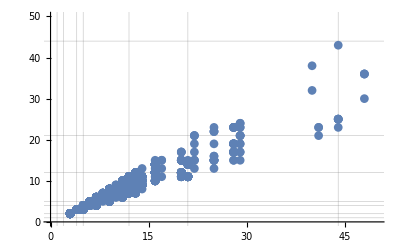

```mathematica
With[
{range=50},
ListPlot[Map[Tooltip[{#[[1]],#[[2]]}/24,#[[3]]]&,comp],PlotRange->{{0,range},{0,range}},PlotMarkers->Automatic, GridLines->{Jacobsthal,Jacobsthal}]
]
```

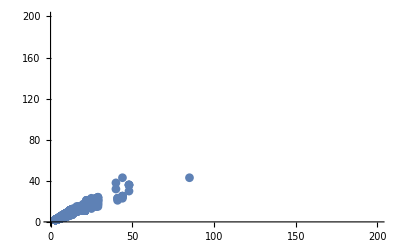

```mathematica
With[
{range=200},
ListPlot[Map[Tooltip[{#[[1]],#[[2]]}/24,#[[3]]]&,comp],PlotRange->{{0,range},{0,range}},PlotMarkers->Automatic]
]
```

```mathematica
ListPlot[Map[Tooltip[{#[[1]],#[[2]]}/24,#[[3]]]&,comp],PlotRange->{{0,range},{0,range}},PlotMarkers->Automatic]
```

```mathematica
$HistoryLength=1
```

1

```mathematica
ChromaticPolynomial[ReadGrof[8468],4]
```

2040

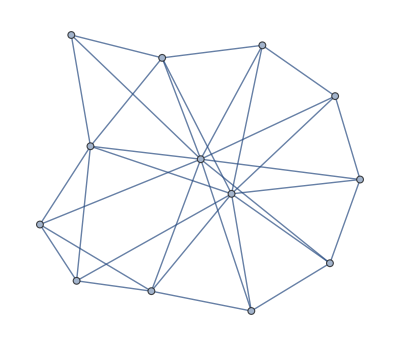

```mathematica
Rule2[ReadGrof[8468],3<->9]
```

```mathematica
IsomorphicGraphQ[Rule2[ReadGrof[8468],3<->9],ReadGrof[57653]]
```

False

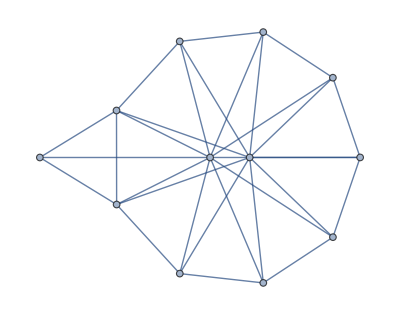

```mathematica
ReadGrof[8468]
```

```mathematica
ChromaticPolynomial[ReadGrof[57653],4]
```

120

```mathematica
Rule2[ReadGrof[8468],3<->9]
```

-Graphics-

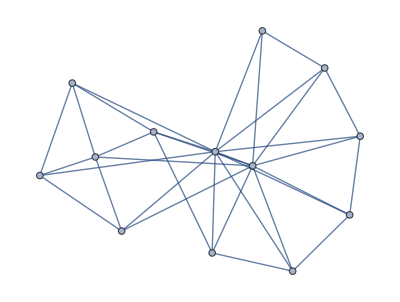

```mathematica
ReadGrof[57653]
```

```mathematica
Take[deps2,5]
```

{{1,2,{2,1<->4}},{1,3,{2,2<->4}},{2,3,{2,2<->4}},{2,4,{2,3<->4}},{2,5,{2,4<->5}}}

```mathematica
deps2=ReadList["D:\\Grofs\\dependencies2.txt",Expression, gmax];Length[deps2]
```

27400

```mathematica
Table[
With[{
from=a[[1]],
to=a[[2]],
edge=Read[StringToStream[ a[[3]]],Expression][[2]],
edge2=Read[StringToStream[ a[[3]]],Expression][[3]]
},

IsomorphicGraphQ[Rule2[ReadGrof[from],edge, edge2],ReadGrof[to]]
],{a,Take[deps2,100]}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Take[deps2,3]
```

{{1,2,{2,1<->4}},{2,3,{2,2<->4}},{2,4,{2,2<->5}}}

```mathematica
IsomorphicGraphQ[Rule2[ReadGrof[2],2<->5,1<->4],ReadGrof[4]]
```

True

```mathematica
VertexCount[ReadGrof[2]]
```

5

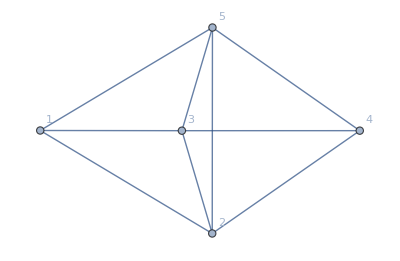

```mathematica
Graph[ReadGrof[2],VertexLabels->"Name"]
```

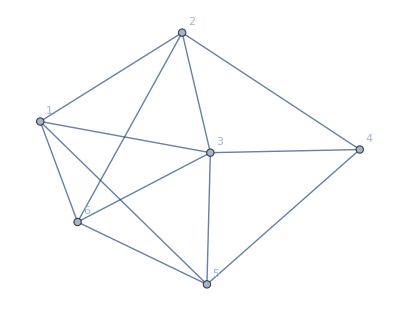

```mathematica
Graph[Rule2[ReadGrof[2],2<->5],VertexLabels->"Name"]
```